```mathematica
CreatePalette[Column[{Button["Hide code",{NotebookFind[SelectedNotebook[],"Output",All,CellStyle];
FrontEndExecute[FrontEndToken[SelectedNotebook[],"SelectionCloseUnselectedCells"]]}],Button["Show code",NotebookFind[SelectedNotebook[],"Input",All,CellStyle]]}]]
```

# Introduction to Quantum Interference

Interference is an important wave phenomenon - and an essential concept in both classical and quantum physics. In this notebook, we will explore how interference figures in quantum theory.

## What is a Wave

Waves are prominent in the natural world, from water waves to electromagnetic waves. Mathematically, a wave is described by periodic motion.

Sine Wave:



```mathematica
Plot[Sin[x],{x,0,2 Pi}]
```

Waves don’t have to be differentiable at every point.

Triangle Wave:

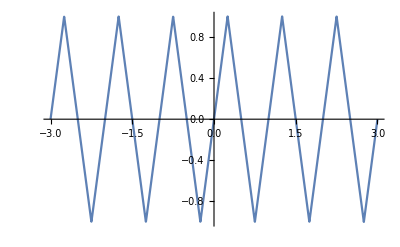

```mathematica
Plot[TriangleWave[x], {x, -3, 3}, ExclusionsStyle -> Dotted]
```

In fact, waves don’t even have to be continuous.

Square Wave:

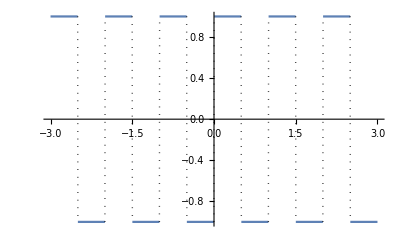

```mathematica
Plot[SquareWave[x], {x, -3, 3}, ExclusionsStyle -> Dotted]
```

## Wave Properties

The period b of a wave is how long it takes to complete one full cycle.

```mathematica
Manipulate[Plot[Sin[2π x/b],{x,0,5}, PlotLabel-> "Sine Wave with Adjustable Period"],{{b,1,"Period"},1,5}]
```

The phase ϕ  translates the wave horizontally.

```mathematica
Manipulate[Plot[Sin[x + ϕ],{x,0,4π}, PlotLabel-> "Sine Wave with Adjustable Phase"],{{ϕ,0,"Phase"},0,2π}]
```

The amplitude A stretches or shrinks the wave vertically.

```mathematica
Manipulate[Plot[A Sin[x ],{x,0,2π}, PlotLabel-> "Sine Wave with Adjustable Amplitude", PlotRange->{{0,2 Pi},{-10,10}}],{{A,1,"Amplitude"},0.5,10}]
```

## Combining Waveforms

When two waves are present, the resulting wave is formed by adding their signed amplitudes at each point. Such a resulting wave is called a linear superposition.

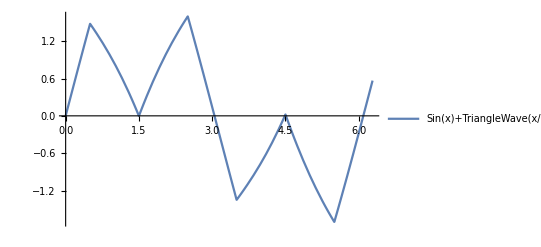
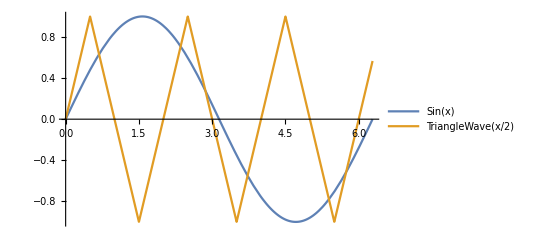

```mathematica
Plot[{Sin[x ],TriangleWave[x/2]},{x,0,2π}, PlotLegends->{"Sin(x)", "TriangleWave(x/2)"}, ImageSize->{400,150}]Plot[Sin[x ]+TriangleWave[x/2],{x,0,2π}, PlotLegends->{"Sin(x)+TriangleWave(x/2)"}, ImageSize->{400,150}]
```

When the signs of the wave amplitudes align, they exhibit constructive interference, and when they oppose each other, they exhibit destructive interference.

Two waves of the same amplitude and period constructively or destructively interfere depending on their relative phase.

```mathematica
Manipulate[{Plot[{Sin[x ],Sin[x + ϕ]},{x,0,2π}, PlotLegends->{"Sin(x)", "Sin(x+ϕ)"}, ImageSize->{400,150}],Plot[Sin[x]+Sin[x + ϕ],{x,0,2π}, PlotLegends->{"Superposition"}, ImageSize->{400,150}, PlotRange->{{0,2 Pi},{-2,2}}]}, "X1"-> {{ϕ, π/2, "relative phase ϕ"},0,2π}]
```

Note that they completely cancel each other when they have a relative phase of ϕ = π

## The Wave Function

In quantum physics, particles are mathematically described by wave functions:

Particle in Infinite Square Well:

```mathematica
wellINF[a_,x_]:= Plot[Piecewise[{{3,x < -a/2},{0,(x>-a/2 && x<a/2)},{3,x>a/2}}], {x,-3,3}, Filling->-3]
psiINF[a_,x_,n_] := Plot[1/Sqrt[2]  Cos[n π x/a],{x,-a/2,a/2},  PlotRange->{{-3,3},{-1,2}}]
Manipulate[Show[wellINF[a,x], psiINF[a,x,n],PlotRange->{{-3,3},{-1,2}}],{{a,4,"Width of Well"},1,5}, {{n,1,"Quantum number"},Range[8]}]
```

Particle in Harmonic Oscillator Potential:

```mathematica
psiQHO[n_, x_]:= Plot[π^(-1/4) Sqrt[(2^n Factorial[n])^(-1)]HermiteH[n,1.3x]Exp[-(1.3x)^2/2],{x,-3,3}]
wellQHO[x_]:= Plot[2/3 x^2,{x,-3,3},Filling->-2]
Manipulate[Show[psiQHO[n,x],wellQHO[x],PlotRange->{{-3,3},{-1,3}}], {{n,0,"Quantum number"},Range[0,8]}]
```

## Exploring Diffraction

Here’s where things get interesting: A particle can actually interfere with ITSELF. Let’s see how this happens.

According to Huygens Principle, every point on a wavefront is a source of wavelets.

```mathematica
wavelets1[t_]:= Graphics[{Table[{Circle[{0,-130},8(n+Mod[t,2]), {0,Pi}]},{n,0,t,2}]},PlotRange->{{-100,100},{-130,-60}},ImageSize->300]
Animate[wavelets1[t],{t,0,12}, AnimationRunning-> True]
```

When a particle passes through a narrow slit, its wavefront propagates radially on the other side of the screen

```mathematica
left1 = Plot[Piecewise[{{-130,x < -2.5 }}], {x,-100,-2.5}, Filling->-135];
right1 = Plot[Piecewise[{{-130,x > 2.5 }}], {x,2.5,100}, Filling->-135];
particle[t_]:= Graphics[Point[{0,Min[20(t+3.5)-200,-130]}]]
```

```mathematica
Animate[Show[left1, right1, particle[t],wavelets1[t],PlotRange-> {{-100,100},{-200,0}}, Frame->None, AspectRatio-> 1, ImageSize-> 300, Axes-> None],{t,-3.5,12},AnimationRunning->True]
```

```mathematica
left2 = Plot[Piecewise[{{-75,x < -15 }}], {x,-100,-15}, Filling->-80];
middle2 = Plot[Piecewise[{{-75,(-10<x && 10 > x) }}], {x,-10,10}, Filling->-80];
right2 = Plot[Piecewise[{{-75,(x > 15) }}], {x,15,100}, Filling->-80];
```

```mathematica
Animate[Show[left1, right1,left2, middle2, right2, wavelets1[t],particle[t],PlotRange-> {{-100,100},{-200,-70}}, Frame->None, AspectRatio->1/2, ImageSize-> 500, Axes-> None],{t,-4,7},AnimationRunning->True]
```

If we place a screen with two more slits in front of the propagating wave, we get two more wave fronts.

```mathematica
screen = Plot[-10,{x,-100,100}];
wavelets2[t_]:= Graphics[{Table[{Circle[{-12.5,-75},8(n+Mod[t,2]), {0,Pi}]},{n,0,t,2}]},PlotRange->{{-72.5,57.5},{-75,-10}},ImageSize->300]
wavelets3[t_]:= Graphics[{Table[{Circle[{12.5,-75},8(n+Mod[t,2]), {0,Pi}]},{n,0,t,2}]},PlotRange->{{-57.5,72.5},{-75,-10}},ImageSize->300]
```

```mathematica
Animate[Show[left2, middle2, right2, wavelets2[t],wavelets3[t],screen, PlotRange-> {{-100,100},{-85,0}}, Frame->None, AspectRatio->1/2, ImageSize-> 500, Axes-> None],{t,-1,8},AnimationRunning->True]
```

At each point on the back screen, the resulting amplitude is the superposition of the waves propagating from both slits.

```mathematica
L = 65;
θ[x_]:= ArcTan[L/(x-12.5)]
```

```mathematica
slitP1[x_]:= Plot[(t -12.5)L/(x-12.5) - 75 ,{t,12.5,x}, PlotRange->{{-100,100},{-85,0}},PlotStyle->Thick,ColorFunction->(Opacity[(Sin[Sqrt[(#-12.5)^2 + ((# -12.5)L/(x-12.5) - 75 )^2 ]]+1)/2,Blue]&), ColorFunctionScaling->False]
slitP2[x_]:= Plot[(t +12.5)L/(x+12.5) - 75 ,{t,x,-12.5}, PlotRange->{{-100,100},{-85,0}},PlotStyle->Thick,ColorFunction->(Opacity[(Sin[Sqrt[(#+12.5)^2 + ((# +12.5)L/(x+12.5) - 75 )^2 ]]+1)/2,Blue]&), ColorFunctionScaling->False]
```

```mathematica
Manipulate[Show[slitP1[x], slitP2[x],left2, middle2, right2,screen, Axes-> None],{{x,0,"Position on screen"},-100,100}]
```

The waves travel different distances to get to any point on the back screen, so by the time they get there they are shifted by some phase ϕ.

## Conclusion

At points where the two wave-fronts differ by a phase of π, they completely destructively interfere, resulting in 0 probability of observing the particle there. This patently non-classical behavior was one of the first indications that a new model (quantum mechanics) was needed to model certain physical phenomena!

Further Exploration

Investigate single slit diffraction where the slit admits a continuum of wave-fronts

Authorship information

Jacob Marks

2017/06/23

jamarks13@gmail.com